# Вывод функции кривой для плавного ограничения параметров, сигналов и не только в Wolfram Mathematica

Существует ряд задач, в которых диапазон выходных значений должен быть ограничен, в то время как входные данные этого гарантировать не могут. Помимо вынужденных ситуаций, ограничение сигнала может быть и целенаправленной задачей - например, при компрессии сигнала или реализации эффекта “overdrive”.

Самая простая реализация ограничения - это принудительная установка в некоторое значение при превышении определённого уровня. Например, для синусоиды с возрастающей амплитудой это будет выглядеть так:

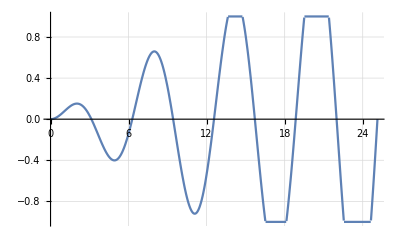

```mathematica
Plot[Clip[ x/12 Sin[x],{-1,1}],{x,0,8Pi},GridLines->Automatic]
```

В роли ограничителя здесь выступает функция Clip, в качестве аргумента которой передаётся входной сигнал и параметры ограничения, а результатом функции является выходной сигнал.

Посмотрим на график функции Clip отдельно:

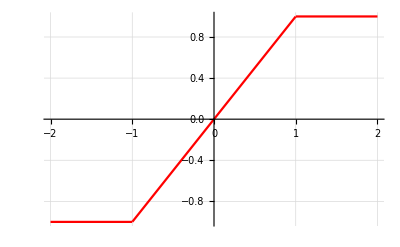

```mathematica
Plot[Clip[ x,{-1,1}],{x,-2,2},GridLines->Automatic,PlotStyle->Red]
```

Из него видно, что пока мы не превышаем пределы ограничения, выходное значение равно входному и сигнал не меняется; при превышении же выходное значение от входного уже никак не зависит и остаётся на одном и том уровне. По сути, мы имеем кусочно-непрерывную функцию, составленную из трёх других: y=-1, y=x и y=1, выбираемых в зависимости от аргумента, и эквивалентную следующей записи:

```mathematica
Piecewise[{{-1,x<-1},{+1,x>1}},x]
```

Piecewise[{{-1, x<-1}, {1, x>1}, {x, True}}]

Переход между функциями происходит довольно резко; и выглядит заманчивым сделать его более плавным. Математически эта резкость обусловлена тем, что производные функций в точках стыковки не совпадают. Это легко увидеть, построив график производной функции Clip:

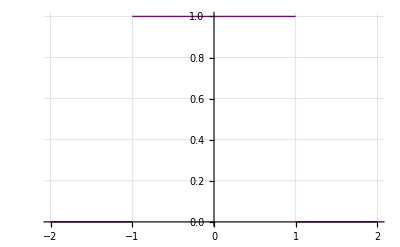

```mathematica
Plot[D[Clip[ x,{-1,1}],x],{x,-2,2},Evaluated->True,PlotStyle->{Purple,Thick},GridLines->Automatic]
```

Таким образом, чтобы обеспечить гладкость функции ограничения, необходимо обеспечить равенство производных в точках стыковки. А поскольку крайние функции у нас константы, производные от которых равны 0, то и производные  функции ограничения в точках стыковки тоже должны быть равны 0. Далее будут  рассмотрены несколько таких функций, обеспечивающих гладкую стыковку.

## Синус

Самое простое - это использовать функцию sin на интервале от -pi/2 до pi/2, на границах которого значения производной равны нулю по определению:

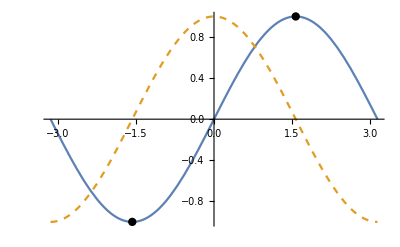

```mathematica
Plot[{Sin[ x],Cos[x]},{x,-Pi,Pi},GridLines->{{-Pi,-Pi/2,Pi/2,Pi},{-1,1}},PlotStyle->{Automatic,Dashed},Epilog->{PointSize[0.015],Point[{{-Pi/2,-1},{Pi/2,1}}]}]
```

Нужно только масштабировать аргументы, чтобы единица отображалась на Pi/2. Теперь мы можем определить собственно ограничивающую функцию:

```mathematica
SinClip[x_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {Sin[(π x)/2], True}}]
```

И построить её график:

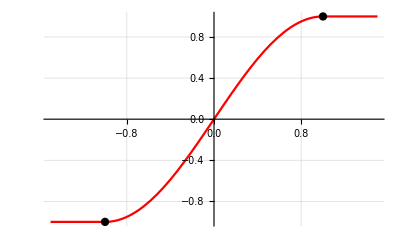

```mathematica
Plot[SinClip[x],{x,-1.5,1.5},GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{1,1}}]},PlotStyle->Red]
```

Так как пределы ограничения у нас жёстко определены, то ограничение задаётся через масштабирование входного сигнала с последующим (при необходимости) обратном масштабировании. 
Здесь также уже нет ситуации, при которой входной сигнал передаётся на выход без искажений - чем меньше уровень усиления, тем меньше уровень искажений вследствие ограничения - но сигнал искажается в любом случае.
Влияние параметра усиления на искажение сигнала можно посмотреть и в динамике:

```mathematica
Manipulate[
Plot[SinClip[k x/12 Sin[x]],{x,0,8Pi},PlotRange->{-1,1},GridLines->Automatic],
{{k,1},0.01,2}]
```

## Больше гладкости

Посмотрим на производную нашей функции:

```mathematica
D[SinClip[ x],x]
```

Piecewise[{{0, x<-1||x==-1}, {1/2 π Cos[(π x)/2], -1<x<1}, {0, True}}]

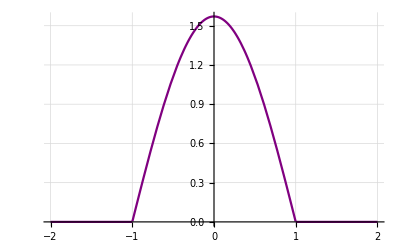

```mathematica
Plot[%,{x,-2,2},PlotStyle->Purple,GridLines->Automatic]
```

В ней уже нет разрывов в значениях, но есть разрывы в производной (второй, если считать от изначальной функции). Для того, чтобы её устранить, можно пойти обратным путём - сначала сформировать гладкую производную, а затем её проинтегрировать для получения искомой функции.
Самый простой способ обнулить производную точках -1 и 1 - это просто возвести функцию в квадрат - все отрицательные значения функции станут положительными и, соответственно, возникнут перегибы в точках пересечения функции с нулём.

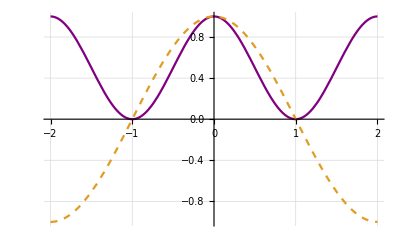

```mathematica
Plot[{Cos[x Pi/2]^2,Cos[x Pi/2]},{x,-2,2},PlotStyle->{Purple,Dashed},GridLines->Automatic]
```

Находим первообразную:

```mathematica
Integrate[Cos[x Pi/2]^2,x]
```

x/2+Sin[π x]/(2 π)

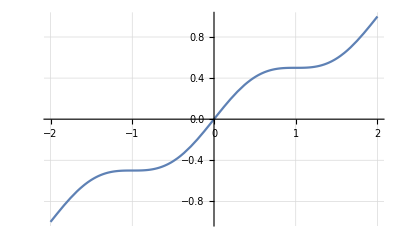

```mathematica
Plot[%,{x,-2,2},GridLines->Automatic]
```

Теперь осталось масштабировать её по оси ординат. Для этого найдём её значение в точке 1:

```mathematica
x/2+Sin[π x]/(2 π)/.x->1
```

1/2

И поделим на неё (да, конкретно здесь это элементарное умножение на 2, но далеко не всегда так бывает):

```mathematica
(x/2+Sin[π x]/(2 π))/(1/2)//Simplify
```

x+Sin[π x]/π

Таким образом, итоговая функция ограничения примет вид:

```mathematica
SoftSinClip[x_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {x+Sin[π x]/π, True}}]
```

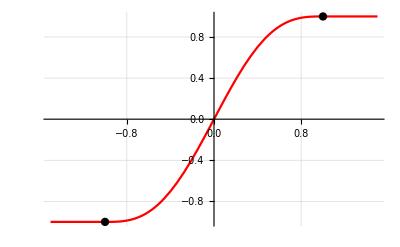

```mathematica
Plot[SoftSinClip[x],{x,-1.5,1.5},GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{1,1}}]},PlotStyle->Red]
```

## Переходим на полиномы

Использование тригонометрический функций в некоторых случаях может оказаться несколько расточительным. Поэтому попробуем построить необходимую нам функцию, оставаясь в рамках элементарных математических операций.
Рассмотрим параболу:

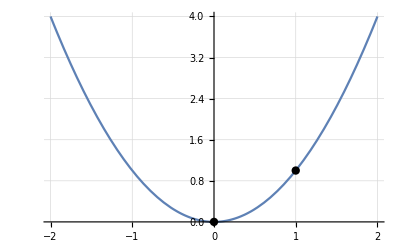

```mathematica
Plot[x^2,{x,-2,2},Epilog->{PointSize[0.015],Point[{{0,0},{1,1}}]}, GridLines->Automatic]
```

Так как у неё уже есть перегиб в точке ноль, мы можем использовать одну и ту же часть на интервале {0,1} для для стыковки с константами. Для отрицательных значений её нужно сместить вниз и влево:

```mathematica
(x^2/.x->x+1)-1//Simplify
```

x (2+x)

а для положительных - отразить по вертикали и горизонтали:

```mathematica
1-(x^2/.x->1-x)//Simplify
```

-(-2+x) x

И наша функция с параболой примет вид:

```mathematica
ParabolClip[x_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {x (2-x), 0≤x<1}, {x (2+x), True}}]
```

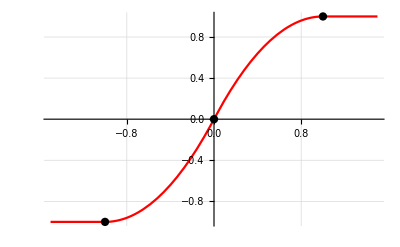

```mathematica
Plot[ParabolClip[x],{x,-1.5,1.5},Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},GridLines->Automatic,PlotStyle->Red]
```

## Немного усложним

Вернёмся к нашей параболе, перевернём её и сместим на единицу вверх:

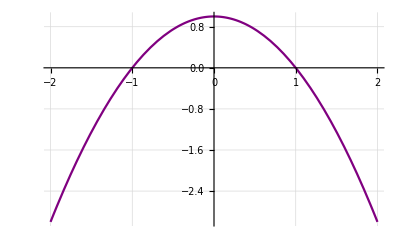

```mathematica
Plot[1-x^2,{x,-2,2},PlotStyle->Purple,GridLines->Automatic]
```

Это будет производная нашей функции. Чтобы сделать её более гладкой в точках стыковки, возведём в квадрат, обнулив таким образом вторую производную:

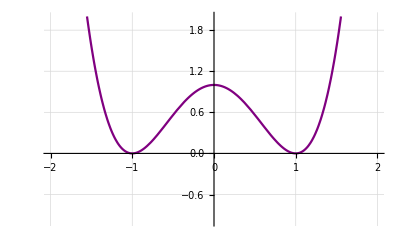

```mathematica
Plot[(1-x^2)^2,{x,-2,2},PlotRange->{-1,2},PlotStyle->Purple,GridLines->Automatic]
```

Интегрируем и масштабируем:

```mathematica
Integrate[(1-x^2)^2,x]//#/(#/.x->1)&//Simplify
```

1/8 x (15-10 x^2+3 x^4)

Получаем ещё более гладкую функцию:

```mathematica
SoftParabolClip[x_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {1/8 x (15-10 x^2+3 x^4), True}}]
```

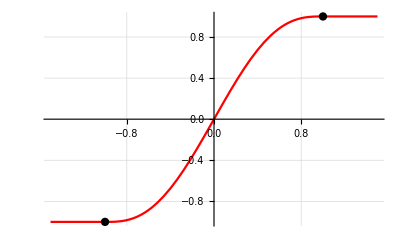

```mathematica
Plot[SoftParabolClip[x],{x,-1.5,1.5},Epilog->{PointSize[0.015],Point[{{-1,-1},{1,1}}]},GridLines->Automatic,PlotStyle->Red]
```

## Больше гладкости богу гладкости

Здесь мы попробуем добиться гладкости в точках стыковки на ещё более высших производных. Для этого для начала определим функцию как полином с неизвестными коэффициентами, а сами коэффициенты попробуем найти через решение системы уравнений.

Начнём со 1-й производной:

```mathematica
f= x+Subscript[a, 3] x^3;
sf=Solve[
{
(D[f,x]/.x->1)==0
}
,{Subscript[a, 3]}]
```

{{a_3→-1/3}}

2-я:

```mathematica
f= x+Subscript[a, 3] x^3+Subscript[a, 5] x^5;
sf=Solve[
{
(D[f,x]/.x->1)==0,
(D[f,{x,2}]/.x->1)==0
}
,{Subscript[a, 3],Subscript[a, 5]}]
```

{{a_3→-2/3,a_5→1/5}}

3-я:

```mathematica
f= x+Subscript[a, 3] x^3+Subscript[a, 5] x^5+Subscript[a, 7] x^7;
sf=Solve[
{
(D[f,x]/.x->1)==0,
(D[f,{x,2}]/.x->1)==0,
(D[f,{x,3}]/.x->1)==0
}
,{Subscript[a, 3],Subscript[a, 5],Subscript[a, 7]}]
```

{{a_3→-1,a_5→3/5,a_7→-1/7}}

Все эти коэффициенты выглядит так, как будто в них есть какая-то логика. Выпишем множители, помножив их на значение степени при х; а чтобы не писать каждый раз одно и  тоже, автоматизируем процесс нахождения  коэффициентов:

```mathematica
Column[Table[Block[
{f=x+∑_(i=1)^n Subscript[a, 2i+1] x^(2i+1)},
s=Solve[Table[(D[f,{x,i}]/.x->1)==0,{i,1,n}],Table[Subscript[a, 2i+1],{i,1,n}]];
ss=Flatten[{1,Table[(2i+1)Subscript[a, 2i+1]//Abs,{i,1,n}]/.s}]]
,{n,1,11}],Center]
```

{1,1}
{1,2,1}
{1,3,3,1}
{1,4,6,4,1}
{1,5,10,10,5,1}
{1,6,15,20,15,6,1}
{1,7,21,35,35,21,7,1}
{1,8,28,56,70,56,28,8,1}
{1,9,36,84,126,126,84,36,9,1}
{1,10,45,120,210,252,210,120,45,10,1}
{1,11,55,165,330,462,462,330,165,55,11,1}

Похоже  [https://oeis.org/search?q=1%2C+11%2C+55%2C+165%2C+330%2C+462%2C+462%2C+330%2C+165%2C+55%2C+11%2C+1&sort=&language=english&go=Search] на биномиальные коэффициенты. Сделаем смелое предположение, что это они и есть, и исходя из этого, запишем обобщённую формулу:

```mathematica
polybin[n_]:=∑_(i=1)^n x^(2i-1)/(2i-1)*(-1)^(i+1)*Binomial[n-1,i-1]
```

Проверим:

```mathematica
Table[D[polybin[10],{x,i}]/.x->{-1,1},{i,1,10}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{185794560,-185794560}}

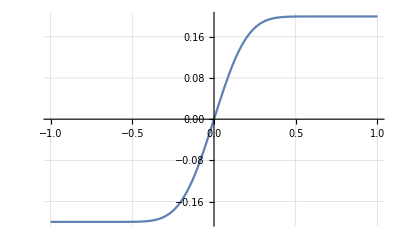

```mathematica
Plot[polybin[20],{x,-1,1},Evaluated->True,GridLines->Automatic]
```

Похоже на правду [*1]. Осталось только посчитать масштабный коэффициент, чтобы привести края к единице:

```mathematica
∑_(i=1)^n 1/(2i-1)*(-1)^(i+1)*Binomial[n-1,i-1]//FullSimplify
```

(√π Gamma[n])/(2 Gamma[1/2+n])

А после масштабирования и упрощения мы обнаружим, что наши познания в математике несколько устарели [*2]:

```mathematica
∑_(i=1)^n x^(2i-1)/(2i-1)*(-1)^(i+1)*Binomial[n-1,i-1]/((√π Gamma[n])/(2 Gamma[1/2+n]))//Simplify
```

(2 x Gamma[1/2+n] Hypergeometric2F1[1/2,1-n,3/2,x^2])/(√π Gamma[n])

Таким образом, мы получили обобщающую функцию порядка n, в которой n-1 первых производных будут равны нулю:

```mathematica
PolySoft[x_,n_]:=(2 x Gamma[1/2+n] Hypergeometric2F1[1/2,1-n,3/2,x^2])/(√π Gamma[n])
```

```mathematica
SoftPolyClip[x_,n_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {PolySoft[x,n], True}}]
```

Посмотрим, что получилось:

```mathematica
Column[Table[PolySoft[x,i],{i,1,10}],Center]
```

x
1/2 x (3-x^2)
1/8 x (15-10 x^2+3 x^4)
1/16 x (35-35 x^2+21 x^4-5 x^6)
1/128 x (315-420 x^2+378 x^4-180 x^6+35 x^8)
1/256 x (693-1155 x^2+1386 x^4-990 x^6+385 x^8-63 x^10)
(x (3003-6006 x^2+9009 x^4-8580 x^6+5005 x^8-1638 x^10+231 x^12))/1024
(x (6435-15015 x^2+27027 x^4-32175 x^6+25025 x^8-12285 x^10+3465 x^12-429 x^14))/2048
(x (109395-291720 x^2+612612 x^4-875160 x^6+850850 x^8-556920 x^10+235620 x^12-58344 x^14+6435 x^16))/32768
(x (230945-692835 x^2+1662804 x^4-2771340 x^6+3233230 x^8-2645370 x^10+1492260 x^12-554268 x^14+122265 x^16-12155 x^18))/65536

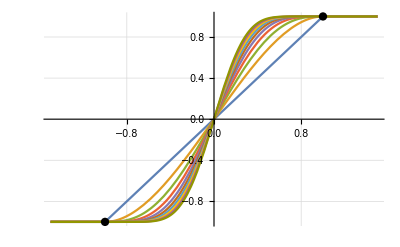

```mathematica
Plot[Table[SoftPolyClip[x,i],{i,1,10}],{x,-1.5,1.5},Evaluated->True,GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{1,1}}]}]
```

И поскольку наша обобщённая формула получилась непрерывной, при желании можно использовать и нецелые значения параметров:

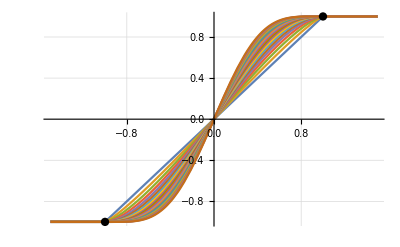

```mathematica
Plot[Table[SoftPolyClip[x,i],{i,1,5,1/5}],{x,-1.5,1.5},Evaluated->True,GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{1,1}}]}]
```

Также можно построить графики производных, приведённых к одному масштабу:

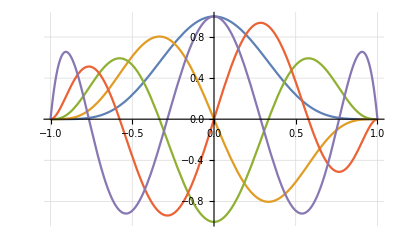

```mathematica
Block[{n=5},
Plot[Table[
D[PolySoft[x,n+1],{x,i}]/((2^i Gamma[i/2] Gamma[3/2+n])/(π Gamma[3/2-i/2+n])),{i,1,n}]//Evaluate
,{x,-1,1},GridLines->Automatic]]
```

## Добавляем жёсткости

Было бы заманчиво, иметь возможность регулировать и степень “жёсткости” ограничения.
Вернёмся к нашей перевёрнутой параболе и добавим коэффициент при степени x:

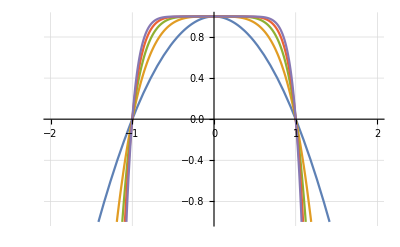

```mathematica
Plot[Table[ 1-x^(2n),{n,1,5}],{x,-2,2},PlotRange->{-1,1},Evaluated->True,GridLines->Automatic]
```

Чем больше n, тем больше наша производная “квадратная”, а её первообразная - соответственно, резкая:

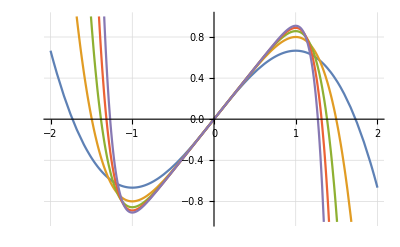

```mathematica
Plot[Table[Integrate[ 1-x^(2n),x],{n,1,5}],{x,-2,2},PlotRange->{-1,1},Evaluated->True,GridLines->Automatic]
```

Посчитаем первообразную и скорректируем масштаб:

```mathematica
Integrate[ 1-x^(2n),x]//#/(#/.x->1)&//Simplify
```

(x (1+2 n-x^(2 n)))/(2 n)

Попробуем теперь задать дробный шаг для параметра:

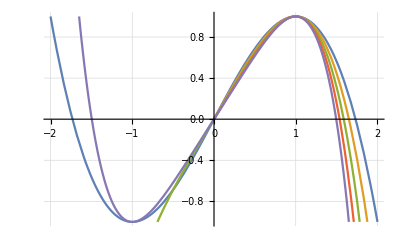

```mathematica
Plot[Table[(x(1+2 n-x^(2 n)))/(2 n),{n,1,2,1/4}],{x,-2,2},PlotRange->{-1,1},Evaluated->True,GridLines->Automatic]
```

Как видим, в отрицательной части не для всех n имеется корректное решение, но в правой (положительной) части необходимые нам условия по-прежнему соблюдаются - поэтому для отрицательных значений мы можем просто использовать её в перевёрнутом виде с реверсированным аргументом. И поскольку область определения параметра уже не ограничена только положительными целыми числами, то можно упростить формулу, заменив 2n на n:

```mathematica
(x(1+2 n-x^(2 n)))/(2 n)/.n->n/2
```

(x (1+n-x^n))/n

А заменив n на n-1, можно сделать формулу чуть более красивой:

```mathematica
(x(1+n-x^n))/n/.n->n-1//Simplify
```

(n x-x^n)/(-1+n)

```mathematica
ClipPolyHard[x_,n_]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {((-x)^n+n x)/(-1+n), -1<x<0}, {(n x-x^n)/(-1+n), True}}]
```

```mathematica
Manipulate[
Plot[ClipPolyHard[x,n],{x,-1.5,1.5},GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},PlotStyle->Red]
,{{n,3},0.1,10}]
```

Поскольку при n равным единице мы получаем деление на ноль, то попробуем найти предел:

```mathematica
Limit[(n x-x^n)/(n-1),n->1]
```

x-x Log[x]

Предел находится, а значит, теперь можно доопределить [*3] функцию для n равным 1 и рассматривать её для всех n больших нуля:

```mathematica
ClipPolyHard[x_,1]:=Piecewise[{{-1, x≤-1}, {1, x≥1}, {x-x Log[Abs[x]], True}}]
```

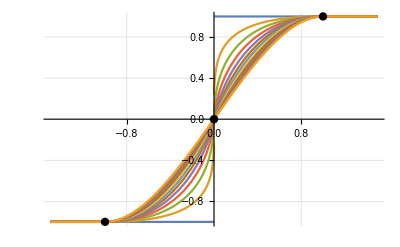

```mathematica
Plot[Table[ClipPolyHard[x,n],{n,0,3,1/4}],{x,-1.5,1.5},GridLines->Automatic,
Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},Evaluated->True]
```

Если же мы изначально возведём нашу перевёрнутую параболу в квадрат, то получим ещё более гладкую функцию:

```mathematica
ClipPolyHard2[x_,n_]:=
Piecewise[{{-1, x≤-1}, {1, x≥1}, {Piecewise[{{x(n+n^2+Abs[x]^(-1+n) (1+n-4 n Abs[x]^(1/2-n/2)))/(-1+n)^2, n≠1}, {1/2 x (2-2 Log[Abs[x]]+Log[Abs[x]]^2), True}}], True}}]
```

И можем сравнить их на одном графике:

```mathematica
Manipulate[
Plot[{
ClipPolyHard[x,n],
ClipPolyHard2[x,n2]
},{x,-1.5,1.5},Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},GridLines->Automatic,PlotStyle->{Red,Blue}],{{n,3},0.1,20},{{n2,8.9},0.1,20}]
```

## Рационализируй это

Посмотрим на следующую функцию:

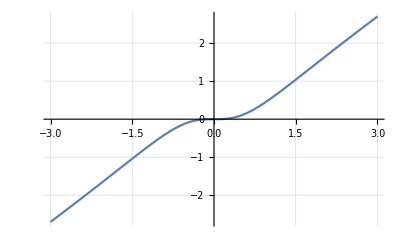

```mathematica
Plot[x^3/(1+x^2),{x,-3,3},GridLines->Automatic]
```

Появилась она не случайно.
Если убрать из неё единицу, x^2 сократится и останется просто x, т.е наклонная прямая. Таким образом, чем меньше значение x, тем большее влияние оказывает единица в знаменателе, создавая необходимое нам искривление. А рассматривая эту функцию в разных масштабах, можно контролировать степень этого искривления:

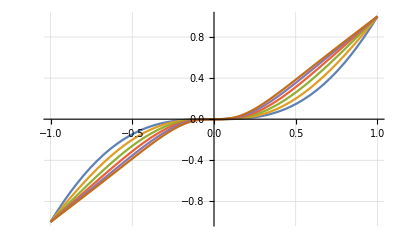

```mathematica
Plot[Table[(k x)^3/(1+(k x)^2)/((k)^3/(1+(k)^2)),{k,0.5,3,0.5}],{x,-1,1},Evaluated->True,GridLines->Automatic]
```

Таким образом, мы можем переписать предыдущую функцию с контролем жёсткости,  используя только рациональный полином 3-порядка:

```mathematica
RationalPolyClip[x_,k_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {-1+((1+k^2) (1+x)^3)/(1+k^2 (1+x)^2), -1≤x<0}, {1+((1+k^2) (-1+x)^3)/(1+k^2 (-1+x)^2), True}}]
```

```mathematica
Manipulate[Plot[RationalPolyClip[x,n],{x,-1.5,1.5},Evaluated->True,GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},PlotStyle->Red],{{n,3},0.1,10}]
```

## Автоматизируй это

Чтобы не задавать каждый раз кусочно-непрерывные функции, мы можем определить вспомогательную функцию, которая сделает это самостоятельно, принимая на вход донорскую функцию в качестве аргумента.

Если наша функция уже обладает диагональной симметрией и выровнена по центру координат (как синусоида), то можно сделать просто

```mathematica
MakeClipSFunction[f_,x_,xscale_]:=Piecewise[{
{-1,x<-1},{1,x>1}},
(f/.x:>x xscale)/(f/.x:>xscale)
]//FullSimplify
```

Пример использования:

```mathematica
MakeClipSFunction[Sin[x],x,Pi/2]
```

Piecewise[{{-1, x<-1}, {1, x>1}, {Sin[(π x)/2], True}}]

Если же нужно собирать из кусочков, как в случае с параболой, и центр координат определяет точки стыковки, то формула слегка усложнится:

```mathematica
MakeClipUFunction[f_,x_,xscale_]:=f-(f/.x:>0)//(#/.x:>x xscale)/(#/.x:>xscale)&//
Piecewise[{
{-1,x<-1},{1,x>1},
{-1+(#/.x:>x+1),-1≤x<0},
{1-(#/.x:>1-x),True}
}]&//FullSimplify
```

Пример использования:

```mathematica
MakeClipUFunction[x^2,x,1]
```

Piecewise[{{-1, x<-1}, {1, x>1}, {-(-2+x) x, 0≤x≤1}, {x (2+x), True}}]

## Перейдём на экспоненту

Совершенно любая функция может быть донором для решения этой задачи, нужно лишь только обеспечить ей точки перегиба. Возьмём, например, сдвинутую вниз на единицу экспоненту:

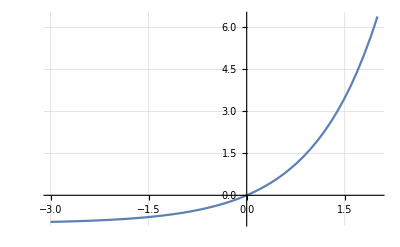

```mathematica
Plot[E^x-1,{x,-3,2},GridLines->Automatic]
```

Ранее, для обеспечения необходимого перегиба в точке ноль, мы возводили функцию в квадрат. Но можно пойти и другим путём - например, суммировать с другой функцией, производная которой в точке ноль противоположна по знаку с производной экспоненты. Например, -x:

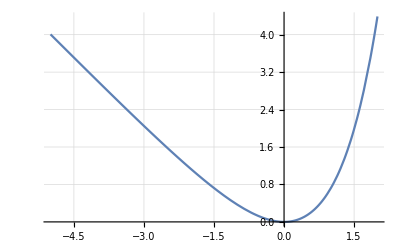

```mathematica
Plot[E^x-1-x,{x,-5,2},GridLines->Automatic]
```

В зависимости от того, с какой стороны мы будем брать кривую, будет и зависеть итоговый вид функции. Теперь, воспользовавшись ранее определённой вспомогательной функцией и выбрав одну из сторон, получим:

```mathematica
ExpClipA[x_,k_]:=(MakeClipUFunction[E^x-1-x,x,k]//Evaluate)
```

```mathematica
ExpClipA//Definition
```

ExpClipA[x_,k_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {(ⅇ^k-ⅇ^(k-k x)-k x)/(-1+ⅇ^k-k), 0≤x≤1}, {(ⅇ^k-ⅇ^(k+k x)+k x)/(1-ⅇ^k+k), True}}]

Либо

```mathematica
ExpClipB[x_,k_]:=(MakeClipUFunction[E^x-1-x,x,-k]//Evaluate)
```

```mathematica
ExpClipB//Definition
```

ExpClipB[x_,k_]:=Piecewise[{{-1, x<-1}, {1, x>1}, {-1+(-1+ⅇ^(-k (1+x))+k+k x)/(-1+ⅇ^-k+k), -1≤x<0}, {(1-ⅇ^(k x)+ⅇ^k k x)/(1+ⅇ^k (-1+k)), True}}]

И теперь можем сравнить их на одном графике:

```mathematica
Manipulate[Plot[{
ExpClipA[x,k],
ExpClipB[x,k]
},{x,-1.5,1.5},Evaluated->True,GridLines->Automatic,Epilog->{PointSize[0.015],Point[{{-1,-1},{0,0},{1,1}}]},PlotStyle->{Red,Blue}],{{k,3},0.1,10}]
```

Видно, что при k -> 0 они стремятся к совпадению; и так как напрямую посчитать их значения мы не можем, поскольку получим деление на ноль, то воспользуемся пределом:

```mathematica
Limit[{ExpClipA[x,k],ExpClipB[x,k]},k->0]
```

{Piecewise[{{-1, x<-1}, {1, x>1}, {-(-2+x) x, 0≤x≤1}, {x (2+x), True}}],Piecewise[{{-1, x<-1}, {1, x>1}, {-(-2+x) x, 0≤x≤1}, {x (2+x), True}}]}

И получили уже известную нам кусочную функцию из параболы.

## Нарушая симметрию

Пока что мы рассматривали исключительно симметричные функции. Однако бывают случаи, когда симметрия нам не нужна - например, для имитации искажений при звучании ламповых усилителей.
Возьмём экспоненту и умножим её на перевёрнутую параболу в квадрате - чтобы получить пересечение с осью абсцисс в точках -1 и 1, а заодно и обеспечить гладкость второй производной; параметризацию же осуществим через масштабирование аргумента экспоненты:

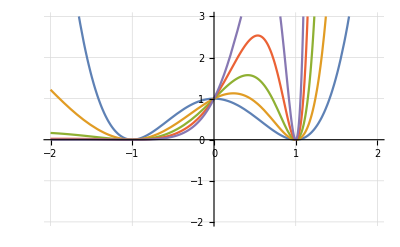

```mathematica
Plot[{Table[
E^(k x)*(1-x^2)^2
,{k,0,4}]
},{x,-2,2},PlotRange->{-2,3},Evaluated->True,GridLines->Automatic]
```

Найдём первообразную и масштабируем её:

```mathematica
ae=Integrate[E^(k x)*(1-x^2)^2,x]//Rescale[#,{#/.x:>-1,#/.x:>1},{-1,1}]&//Simplify
```

-(-4 ⅇ^(2 k) (3-3 k+k^2)-4 (3+3 k+k^2)+ⅇ^(k+k x) (24-24 k x-4 k^3 x (-1+x^2)+k^4 (-1+x^2)^2+4 k^2 (-1+3 x^2)))/(4 (3+3 k+k^2-ⅇ^(2 k) (3-3 k+k^2)))

Так как при k=0 получим деление на ноль:

```mathematica
ae/.k->0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

То дополнительно найдём предел,

```mathematica
Limit[ae,k->0]
```

1/8 x (15-10 x^2+3 x^4)

который представляет из себя уже известный нам гладкий полином 3-го порядка. Соединив всё в одну функцию, получим

```mathematica
AsymmetricExpClip[x_,k_]:=
Piecewise[{{-1, x≤-1}, {1, x≥1}, {Piecewise[{{-((-4 ⅇ^(2 k) (3-3 k+k^2)-4 (3+3 k+k^2)+ⅇ^(k+k x) (24-24 k x-4 k^3 x (-1+x^2)+k^4 (-1+x^2)^2+4 k^2 (-1+3 x^2)))/(4 (3+3 k+k^2-ⅇ^(2 k) (3-3 k+k^2)))), k≠0}, {1/8 x (15-10 x^2+3 x^4), True}}], True}}]
```

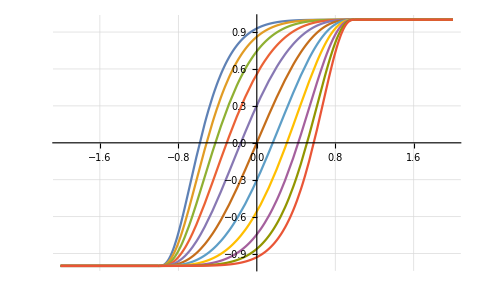

```mathematica
Plot[Table[AsymmetricExpClip[x,k],{k,-5,5}],{x,-2,2},Evaluated->True,GridLines->Automatic]
```

Вместо того, чтобы изначально проектировать асимметричную функцию, можно пойти и другим путём - использовать готовую симметричную, но “искривлять” значение этой функции с помощью дополнительной функции кривой, определённой на промежутке {-1,1}.

Рассмотрим, например, гиперболу:

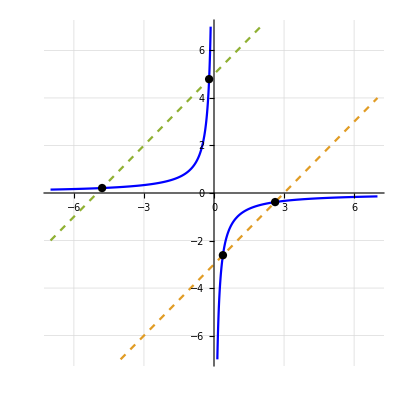

```mathematica
Plot[{
-1/x,x-3,x+5
},{x,-7,7}, GridLines->Automatic,PlotRange->{-7,7},AspectRatio->1,PlotStyle->{{Blue},{Dashed},{Dashed}},Epilog->{PointSize[0.015],Point[{{1/2 (3-√5),-2/(3-√5)},
{1/2 (3+√5),-2/(3+√5)},{1/2 (-5-√21),-2/(-5-√21)},{1/2 (-5+√21),-2/(-5+√21)}}]}]
```

Рассматривая её отрезок в разных масштабах, можно регулировать степень искривления в обе стороны. Как же найти этот отрезок? Исходя из графика, можно было бы искать пересечения гиперболы с прямой. Однако, поскольку такое пересечение существует не всегда, это создаёт некоторые сложности. Поэтому мы пойдём другим путём.

Для начала добавим в гиперболу масштабирующие коэффициенты:

```mathematica
hyp[x_]:=1/(a+b x)+c
```

затем составим систему уравнений, задающих условия прохождения гиперболы через заданные точки - и её решение даст интересующие нас коэффициенты:

```mathematica
s=Solve[{
hyp[-1]==-1,
hyp[1]==1,
hyp[0]==k
},{a,b,c}]
```

{{a→k/(-1+k^2),b→k^2/(-1+k^2),c→1/k}}

Теперь подставим решение в исходную формулу и упростим:

```mathematica
hyp[x]/.s//Simplify
```

{(k+x)/(1+k x)}

```mathematica
HyperbolCurve[x_,k_]:=(k+x)/(1+k x)
```

Посмотрим, что у нас получилось в зависимости от параметра k:

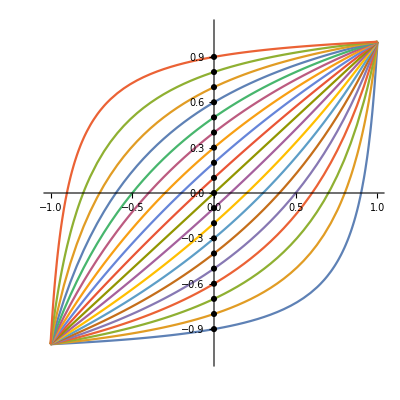

```mathematica
Plot[
Table[HyperbolCurve[x,k],{k,-0.9,0.9,0.1}]
,{x,-1,1},Evaluated->True,PlotRange->{-1.1,1.1},AspectRatio->1,GridLines->{Table[i,{i,-1,1,0.1}]},
Epilog->{PointSize[0.011],Point[Table[{0,i},{i,-0.9,0.9,0.1}]]}]
```

Примечательно, что при k=0 формула естественным образом схлопывается в x и никаких особых ситуаций не происходит - хотя применительно к исходной гиперболе это равносильно отрезку нулевой длины, причём двум сразу. Не менее примечательно, что обратной к ней функцией является она же самая, но с отрицательным параметром k:

```mathematica
HyperbolCurve[HyperbolCurve[x,k],-k]//FullSimplify
```

x

Теперь мы можем использовать её для модификации произвольной функции ограничения, а параметр k таким образом будет задавать точку пересечения с осью ординат:

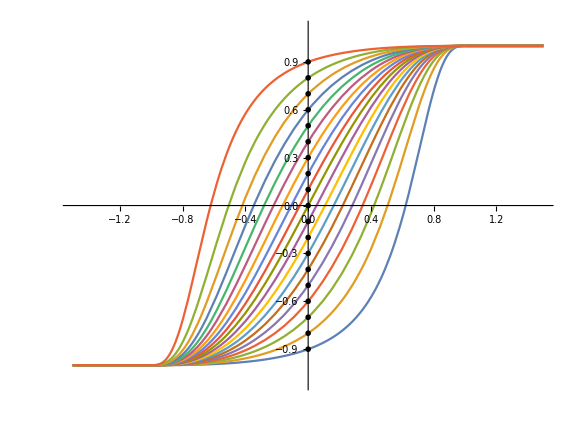

```mathematica
Plot[Table[
HyperbolCurve[SoftParabolClip[x],k]
,{k,-0.9,0.9,0.1}]
,{x,-1.5,1.5},Evaluated->True,PlotRange->{-1.11,1.11},GridLines->{Table[i,{i,-1.5,1.5,0.1}]},Epilog->{PointSize[0.007],Point[Table[{0,i},{i,-0.9,0.9,0.1}]]},ImageSize->Large,AspectRatio->1.11/1.5]
```

Аналогичным образом можно строить кривые и из других функций,  например, степенной с переменным основанием:

```mathematica
ExpCurve[x_,k_]:=Piecewise[{{x, k==0}, {(1+k^2+(-1+k^2) (-1+2/(1+k))^x)/(2 k), True}}]
```

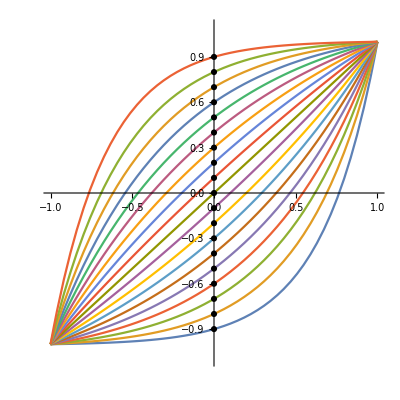

```mathematica
Plot[Table[
ExpCurve[x,k]
,{k,-0.9,0.9,0.1}]
,{x,-1,1},Evaluated->True,PlotRange->{-1.1,1.1},AspectRatio->1,GridLines->{Table[i,{i,-1,1,0.1}]},
Epilog->{PointSize[0.011],Point[Table[{0,i},{i,-0.9,0.9,0.1}]]}]
```

Или обратной к ней логарифмической:

```mathematica
LogCurve[x_,k_]:=Piecewise[{{x, k==0}, {1-(2 Log[1-(2 k (-1+x))/(-1+k)^2])/Log[1+(4 k)/(-1+k)^2], True}}]
```

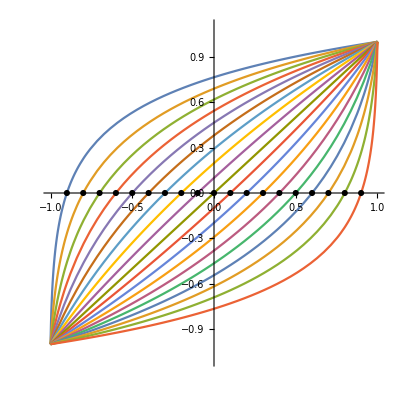

```mathematica
Plot[Table[
LogCurve[x,k]
,{k,-0.9,0.9,0.1}]
,{x,-1,1},Evaluated->True,PlotRange->{-1.1,1.1},AspectRatio->1,GridLines->{Table[i,{i,-1,1,0.1}]},
Epilog->{PointSize[0.011],Point[Table[{i,0},{i,-0.9,0.9,0.1}]]}]
```

## Нужно больше точности

Мы можем захотеть иметь гарантированно линейный промежуток у функции на некотором интервале. Это логично организовать введением прямой линии в кусочно-непрерывную функцию,

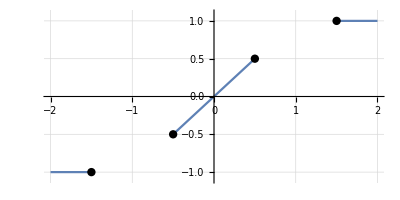

```mathematica
Plot[
Piecewise[{{x,-0.5<x<0.5},{-1,x<-1.5},{1,x>1.5}},Null]
,{x,-2,2},PlotRange->{-1.1,1.1},AspectRatio->1/2,Epilog->{PointSize[0.015],Point[{{-1.5,-1},{-0.5,-0.5},{0.5,0.5},{1.5,1}}]},GridLines->Automatic]
```

пустые места в которой необходимо заполнить какой-нибудь функцией. Очевидно, что для гладкой стыковки с линейным участком её первая производная должна быть равна единице; а все последующие (по возможности) нулю. Чтобы не не выводить такую функцию заново, мы можем взять уже готовую и адаптировать под эту задачу. Также можно заметить, что крайние точки отстоят чуть дальше единицы - это необходимо, чтобы сохранить наклон линейного участка.

Возьмём выведенную ранее функцию PolySoft и сместим её так, чтобы в центре координат получить единицу:

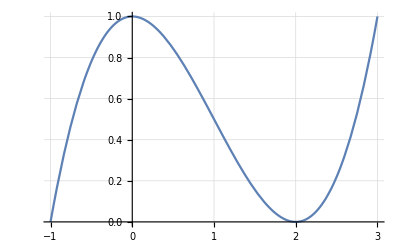

```mathematica
Plot[
(1-PolySoft[x-1,2])/2
,{x,-1,3},GridLines->Automatic]
```

Из её свойств следует, что n-1 последующих производных в точках 0 и 2 будут равны нулю:

```mathematica
Block[{n=6},Table[D[(1-PolySoft[x-1,n])/2,{x,i}],{i,1,n}]]/.{x->{0,2}}
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{-10395/2,10395/2}}

Теперь проинтегрируем её:

```mathematica
f=Integrate[(1-PolySoft[x-1,n])/2,x]//FullSimplify
```

1/2 (x-(Gamma[1/2+n] (-1+(-(-2+x) x)^n+2 n (-1+x)^2 Hypergeometric2F1[1/2,1-n,3/2,(-1+x)^2]))/(√π Gamma[1+n]))

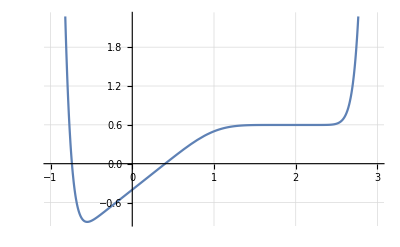

```mathematica
Plot[
f/.n->8
,{x,-1,3},GridLines->Automatic]
```

Функция оказалась сдвинутой вниз относительно оси абсцисс. Поэтому необходимо добавить константу (равную значению функции в точке 0), чтобы совместить центры координат:

```mathematica
f2=f-(f/.x->0)//Simplify
```

1/2 (x+(n Gamma[n])/Gamma[1+n]+(Gamma[1/2+n] (0^n-(-(-2+x) x)^n-2 n (-1+x)^2 Hypergeometric2F1[1/2,1-n,3/2,(-1+x)^2]))/(√π Gamma[1+n]))

Здесь у нас появился ноль в степени n. Он не сократился, так как значение ноль в степени ноль не определено; мы можем его удалить вручную, а можем при упрощении явно указать, что n у нас больше нуля:

```mathematica
f3=FullSimplify[f2,n>0]
```

1/2 (1+x-(Gamma[1/2+n] ((-(-2+x) x)^n+2 n (-1+x)^2 Hypergeometric2F1[1/2,1-n,3/2,(-1+x)^2]))/(√π Gamma[1+n]))

```mathematica
PolyRoll[x_,n_]:=1/2 (1+x-1/(√π Gamma[1+n])Gamma[1/2+n] ((-(-2+x) x)^n+2 n (-1+x)^2 Hypergeometric2F1[1/2,1-n,3/2,(-1+x)^2]))
```

Проверим на всякий случай. Значение в точках 0 и 2 для всех n:

```mathematica
FullSimplify[PolyRoll[{0,2},n],n>0]
```

{0,1}

Производные на краях интервала (для полинома порядка 5):

```mathematica
Table[D[PolyRoll[x,5],{x,i}]//{#/.x->0,#/.x->2}&,{i,1,6}]
```

{{1,0},{0,0},{0,0},{0,0},{0,0},{-945/2,-945/2}}

Как видим функция получилась довольно громоздкой. Чтобы не таскать её и не переусложнять вычисления, дальше будем манипулировать уже с конкретным полиномом, например 4-го порядка:

```mathematica
filler[x_]:=PolyRoll[x,4]//Evaluate//Simplify//Evaluate
```

```mathematica
filler//Definition
```

filler[x_]:=x-(7 x^5)/16+(7 x^6)/16-(5 x^7)/32+(5 x^8)/256

И вот теперь ею можно заполнить свободное пространство:

```mathematica
LinearClip[x_,t_]:=Piecewise[{
{x,-t<x<t},
{t+(1-t)filler[(x-t)/(1-t)],t<x≤2-t},
{-t-(1-t)filler[(-x-t)/(1-t)],-2+t<x<=-t},
{-1,x<-2+t},
{1,x>2-t}
}]
```

Проверим:

```mathematica
Manipulate[
Plot[{LinearClip[x,t]
},{x,-2,2},GridLines->{Table[i,{i,-2,2,1/2}]},Epilog->{PointSize[0.015],Point[{{-2+t,-1},{-t,-t},{2-t,1},{t,t}}]}]
,{{t,0.5},0,0.999}]
```

## Уходим в бесконечность

Иногда может оказаться потребность в функциях, которые стремятся к единице, но не достигают её. Википедия подсказывает [https://ru.wikipedia.org/wiki/%D0%A1%D0%B8%D0%B3%D0%BC%D0%BE%D0%B8%D0%B4%D0%B0] несколько известных решений:

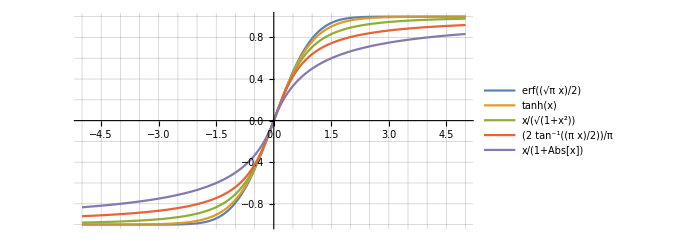

```mathematica
Plot[{
Erf[(√π x)/2],Tanh[x],x/(√(1+x^2)),2/π ArcTan[(π x)/2],x/(1+Abs[x])

},{x,-5,5},PlotLegends->"Expressions",AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500]
```

Так как эти функции единицы не достигают, их удобнее нормировать по производной в центре координат.

Мы можем модифицировать форму таких функции  через их аргумент с помощью какой-нибудь диагонально-симметричной функции, например:

```mathematica
HyperAccelerator[x_,k_]:=Piecewise[{{x, k==0}, {Sinh[k x]/k, k>0}, {ArcSinh[k x]/k, k<0}}]
```

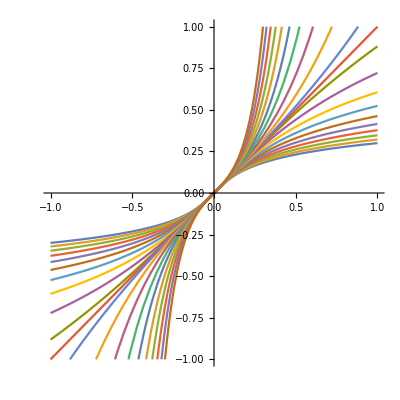

```mathematica
Plot[Table[
HyperAccelerator[x,k]
,{k,-10,10,1}]
,{x,-1,1},Evaluated->True,PlotRange->{-1,1},AspectRatio->1,GridLines->{Table[i,{i,-1.5,1.5,0.1}]}]
```

Эта функция, к слову, также является обратной самой к себе, т.е.

```mathematica
HyperAccelerator[HyperAccelerator[x,k],-k]==x
```

И, применительно к арктангенсу в качестве примера, получим:

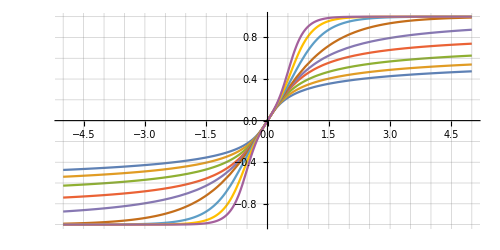

```mathematica
Plot[Table[
2ArcTan[HyperAccelerator[x,k]]/Pi
,{k,-4,4,1}]
,{x,-5,5},Evaluated->True,PlotRange->{-1,1},AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500]
```

что, в частности, с параметром k=1 даст нам функцию Гудермана [https://ru.wikipedia.org/wiki/%D0%A4%D1%83%D0%BD%D0%BA%D1%86%D0%B8%D1%8F_%D0%93%D1%83%D0%B4%D0%B5%D1%80%D0%BC%D0%B0%D0%BD%D0%B0].

Как видим, при таком подходе можно получить нежелательные перегибы, поэтому более предпочтительно контролировать жёсткость ограничения  непосредственно через свойство самой функции. Рассмотрим несколько таких функций с параметром, вывод которых для краткости опустим.

Из степенной функции:

```mathematica
PowerSigmoid[x_,k_]:=x (1+(x^2)^(k/2))^(-1/k)
```

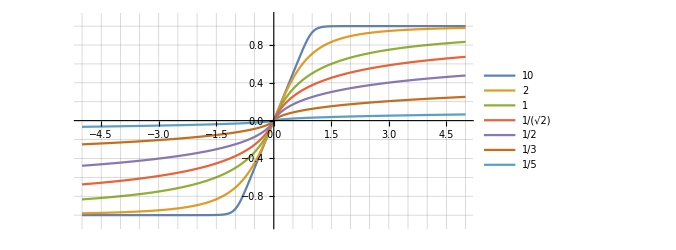

```mathematica
parameters={10,2,1,1/√2,1/2,1/3,1/5};
Plot[Evaluate@Table[
PowerSigmoid[x,k]
,{k,parameters}]
,{x,-5,5},PlotRange->{-1.1,1.1},AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500,PlotLegends->parameters]
```

Из суммы двух v-образных функций со смещением:

```mathematica
RadicalSigmoid[x_,k_]:=(-√(1+(-k+x √(1+k^2))^2)+√(1+(k+x √(1+k^2))^2))/(2k)
```

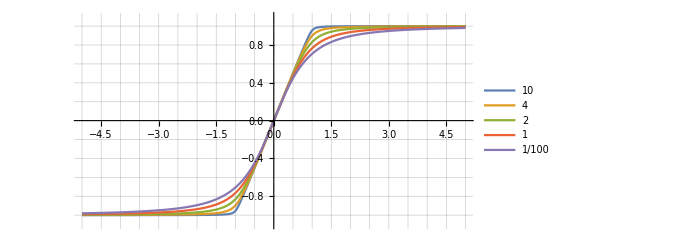

```mathematica
parameters={10,4,2,1,1/100};
Plot[Evaluate@Table[
RadicalSigmoid[x,k]
,{k,parameters}]
,{x,-5,5},PlotRange->{-1.1,1.1},AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500,PlotLegends->parameters]
```

Из обобщённой функции ошибок:

```mathematica
GammaSigmoid[x_,k_]:=Sign[x](1-Gamma[1/k,(x^2 Gamma[1+1/k]^2)^(k/2)]/Gamma[1/k])
```

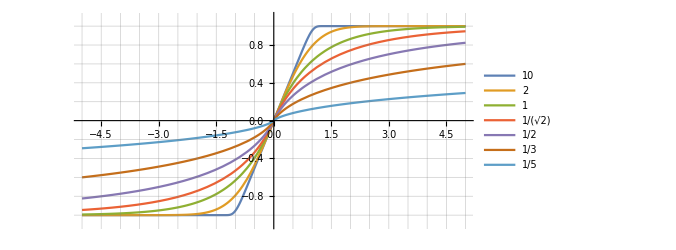

```mathematica
parameters={10,2,1,1/√2,1/2,1/3,1/5};
Plot[Evaluate@Table[
GammaSigmoid[x,k]
,{k,parameters}]
,{x,-5,5},PlotRange->{-1.1,1.1},AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500,PlotLegends->parameters]
```

Интегрированием рационального полинома:

```mathematica
HypergeometricSigmoid[x_,k_]:=x Hypergeometric2F1[1,1/(1+k),1+1/(1+k),-π^(1+k) ((x^2 Csc[π/(1+k)]^2)/(1+k)^2)^((1+k)/2)]
```

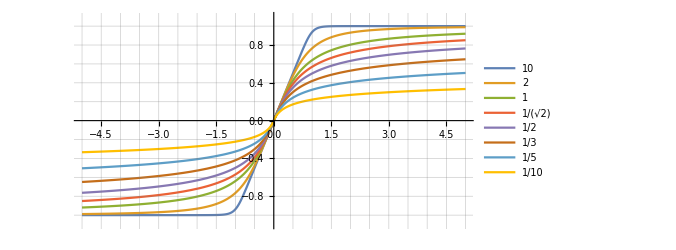

```mathematica
parameters={10,2,1,1/√2,1/2,1/3,1/5,1/10};
Plot[Evaluate@Table[
HypergeometricSigmoid[x,k]
,{k,parameters}]
,{x,-5,5},Evaluated->True,PlotRange->{-1.1,1.1},AspectRatio->1/2,GridLines->{Table[i,{i,-5,5,0.5}],Table[i,{i,-1,1,0.2}]},ImageSize->500,PlotLegends->parameters]
```

Интересно, что её частным случаем является арктангенс:

```mathematica
HypergeometricSigmoid[x,1]//FullSimplify
```

(2 ArcTan[(π x)/2])/π

## Заключение

Построение подобного рода функций может быть увлекательным занятием, в ходе которого будут получаться как простые, так и сложные, как красивые, так и не очень, формулы. Может показаться, что все они сильно друг на друга похожи и надобности в подобном разнообразии нет. Это не обязательно так.
 
Разница может быть сильнее видна в других масштабах - например, логарифмическом.  Кроме того, помимо обозначенных в заголовке задач, подобные функции могут использоваться и в других задачах - смешивании сигналов, когда плавное затухание одного сигнала сочетается с плавным нарастанием другого, или построении акустических  фильтров - и тогда разница будет восприниматься на слух, или же для построения градиентов - и тогда разница будет восприниматься на глаз. Кроме того, они также могут использоваться в качестве доноров для других, более сложных функций - например,  оконных [https://en.wikipedia.org/wiki/Window_function]. 
 
 В завершение стоит уточнить ещё несколько моментов.
 Все функции здесь были определены в диапазоне от -1 до 1. В случае, если нужен другой диапазон (например, от 0 до 1), его легко можно пересчитать либо вручную:

```mathematica
(1+ParabolClip[x])/2//PiecewiseExpand//Simplify
```

Piecewise[{{1, x≥1}, {1/2+x-x^2/2, 0≤x<1}, {1/2 (1+x)^2, -1<x<0}, {0, True}}]

Либо используя встроенную функцию масштабирования:

```mathematica
Rescale[ParabolClip[x],{-1,1},{0,1}]//PiecewiseExpand//Simplify
```

Piecewise[{{1, x≥1}, {1/2+x-x^2/2, 0≤x<1}, {1/2 (1+x)^2, -1<x<0}, {0, True}}]

А для облегчения экспорта полученных формул в программный код может пригодиться функция CForm:

```mathematica
(ⅇ^k-ⅇ^(k-k x)-k x)/(-1+ⅇ^k-k)//CForm
```

(Power(E,k) - Power(E,k - k*x) - k*x)/(-1 + Power(E,k) - k)

Исходный документ Mathematica можно скачать [здесь].

Примечания:
[1] настоящий математик наверняка сможет строго доказать (или опровергнуть) это утверждение
[2] в стандартном курсе мат.анализа гипергеометрические функции не рассматриваются
[3] эта перегрузка определена только для символьной единицы; единица в формате с плавающей точкой (например, при построении графика) распознана не будет.